```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
data = Import["/Users/sm75/github/group-reputations/data/DISC-multiple-prob/data.csv","Dataset",HeaderLines->1];
coop = {"coop_11","coop_12","coop_21","coop_22"};
repsInd = {"reps_ind_11","reps_ind_12","reps_ind_21","reps_ind_22"};
repsGrp = {"reps_grp_11","reps_grp_12","reps_grp_21","reps_grp_22"};
```

```mathematica
d = data[Select[#norm=="SJ"&]][GroupBy["ind_scale"]];
```

```mathematica
Probs = d[1][[All,"prob"]]//Normal//DeleteDuplicates;
```

```mathematica
d
```

Dataset[<>]

```mathematica
{c111,c112,c121,c122}=Table[ Mean @ Values@ Normal[d[1][Select[#prob == p &]][[All,coop]]],{p,Probs}]//Transpose;
{c211,c212,c221,c222}=Table[ Mean @ Values@ Normal[d[2][Select[#prob == p &]][[All,coop]]],{p,Probs}]//Transpose;
{c311,c312,c321,c322}=Table[ Mean @ Values@ Normal[d[3][Select[#prob == p &]][[All,coop]]],{p,Probs}]//Transpose;

{r111,r112,r121,r122}=Table[ Mean @ Values@ Normal[d[1][Select[#prob == p &]][[All,repsInd]]],{p,Probs}]//Transpose;
{r211,r212,r221,r222}=Table[ Mean @ Values@ Normal[d[2][Select[#prob == p &]][[All,repsInd]]],{p,Probs}]//Transpose;
{r311,r312,r321,r322}=Table[ Mean @ Values@ Normal[d[3][Select[#prob == p &]][[All,repsInd]]],{p,Probs}]//Transpose;

{g111,g112,g121,g122}=Table[ Mean @ Values@ Normal[d[1][Select[#prob == p &]][[All,repsGrp]]],{p,Probs}]//Transpose;
{g211,g212,g221,g222}=Table[ Mean @ Values@ Normal[d[2][Select[#prob == p &]][[All,repsGrp]]],{p,Probs}]//Transpose;
{g311,g312,g321,g322}=Table[ Mean @ Values@ Normal[d[3][Select[#prob == p &]][[All,repsGrp]]],{p,Probs}]//Transpose;
```

```mathematica
ticks = Range[0.0,1.0,0.2];
```

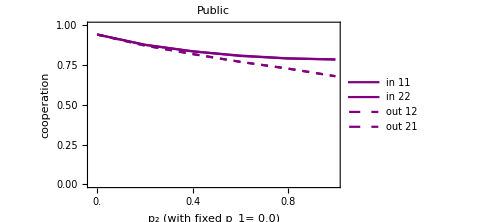

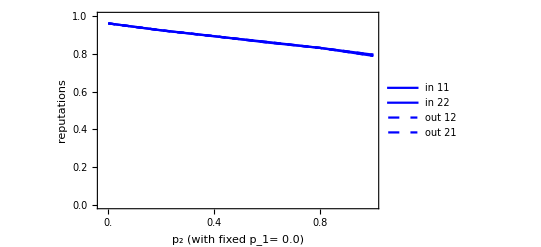

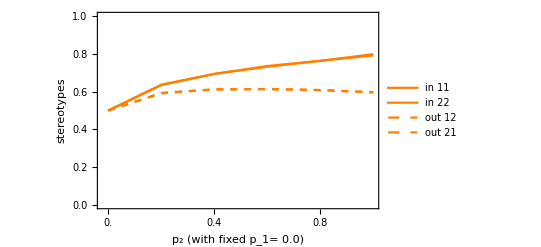

```mathematica
c1 =ListLinePlot[{c111,c122,c112,c121},Frame->True,PlotRange->{All,{0,1}},
FrameTicks-> {Automatic,{Thread[{Range[Length@Probs],ticks}],None}},
FrameLabel->{"p_2 (with fixed p_1= 0.0)","cooperation"},PlotLegends->{"in    11","in    22","out  12","out  21"},
PlotStyle->{Directive[Purple],Directive[Purple],Directive[Purple,Dashed],Directive[Purple,Dashed]},
PlotLabel->"Public",ImageSize->Medium]

r1 = ListLinePlot[{r111,r122,r112,r121},Frame->True,PlotRange->{All,{0,1}},
FrameTicks-> {Automatic,{Thread[{Range[Length@Probs],ticks}],None}},
FrameLabel->{"p_2 (with fixed p_1= 0.0)","reputations"},PlotLegends->{"in    11","in    22","out  12","out  21"},
PlotStyle->{Directive[Blue],Directive[Blue],Directive[Blue,Dashed],Directive[Blue,Dashed]}]

g1 = ListLinePlot[{g111,g122,g112,g121},Frame->True,PlotRange->{All,{0,1}},
FrameTicks-> {Automatic,{Thread[{Range[Length@Probs],ticks}],None}},
FrameLabel->{"p_2 (with fixed p_1= 0.0)","stereotypes"},PlotLegends->{"in    11","in    22","out  12","out  21"},
PlotStyle->{Directive[Orange],Directive[Orange],Directive[Orange,Dashed],Directive[Orange,Dashed]}]
```

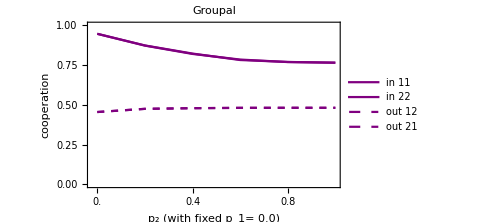

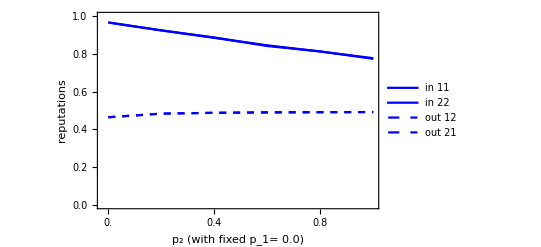

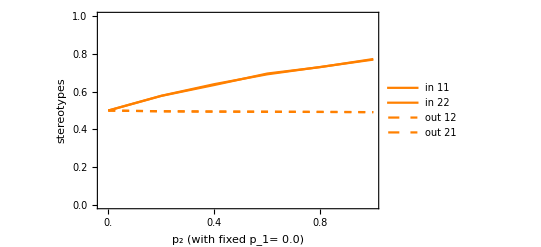

```mathematica
c2 = ListLinePlot[{c211,c222,c212,c221},Frame->True,PlotRange->{All,{0,1}},
FrameTicks-> {Automatic,{Thread[{Range[Length@Probs],ticks}],None}},
FrameLabel->{"p_2 (with fixed p_1= 0.0)","cooperation"},PlotLegends->{"in    11","in    22","out  12","out  21"},
PlotStyle->{Directive[Purple],Directive[Purple],Directive[Purple,Dashed],Directive[Purple,Dashed]},
PlotLabel->"Groupal",ImageSize->Medium]

r2 = ListLinePlot[{r211,r222,r212,r221},Frame->True,PlotRange->{All,{0,1}},
FrameTicks-> {Automatic,{Thread[{Range[Length@Probs],ticks}],None}},
FrameLabel->{"p_2 (with fixed p_1= 0.0)","reputations"},PlotLegends->{"in    11","in    22","out  12","out  21"},
PlotStyle->{Directive[Blue],Directive[Blue],Directive[Blue,Dashed],Directive[Blue,Dashed]}]

g2 = ListLinePlot[{g211,g222,g212,g221},Frame->True,PlotRange->{All,{0,1}},
FrameTicks-> {Automatic,{Thread[{Range[Length@Probs],ticks}],None}},
FrameLabel->{"p_2 (with fixed p_1= 0.0)","stereotypes"},PlotLegends->{"in    11","in    22","out  12","out  21"},
PlotStyle->{Directive[Orange],Directive[Orange],Directive[Orange,Dashed],Directive[Orange,Dashed]}]
```

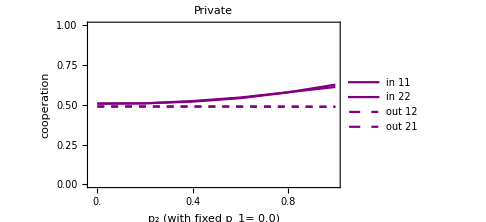

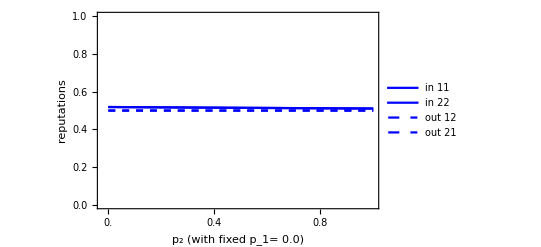

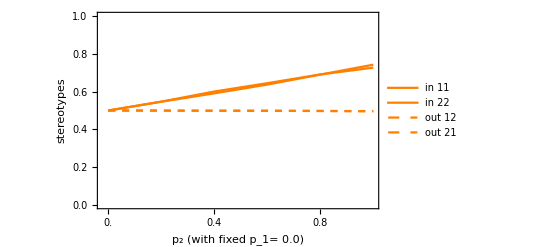

```mathematica
c3 = ListLinePlot[{c311,c322,c312,c321},Frame->True,PlotRange->{All,{0,1}},
FrameTicks-> {Automatic,{Thread[{Range[Length@Probs],ticks}],None}},
FrameLabel->{"p_2 (with fixed p_1= 0.0)","cooperation"},PlotLegends->{"in    11","in    22","out  12","out  21"},
PlotStyle->{Directive[Purple],Directive[Purple],Directive[Purple,Dashed],Directive[Purple,Dashed]},
PlotLabel->"Private",ImageSize->Medium]

r3 = ListLinePlot[{r311,r322,r312,r321},Frame->True,PlotRange->{All,{0,1}},
FrameTicks-> {Automatic,{Thread[{Range[Length@Probs],ticks}],None}},
FrameLabel->{"p_2 (with fixed p_1= 0.0)","reputations"},PlotLegends->{"in    11","in    22","out  12","out  21"},
PlotStyle->{Directive[Blue],Directive[Blue],Directive[Blue,Dashed],Directive[Blue,Dashed]}]

g3 = ListLinePlot[{g311,g322,g312,g321},Frame->True,PlotRange->{All,{0,1}},
FrameTicks-> {Automatic,{Thread[{Range[Length@Probs],ticks}],None}},
FrameLabel->{"p_2 (with fixed p_1= 0.0)","stereotypes"},PlotLegends->{"in    11","in    22","out  12","out  21"},
PlotStyle->{Directive[Orange],Directive[Orange],Directive[Orange,Dashed],Directive[Orange,Dashed]}]
```

```mathematica
{c1,c2,c3}//TableForm
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
GraphicsGrid[{{r1,r2,r3},{g1,g2,g3}}]
```

-Graphics-